# Dynamics of photoinduced PCET

## Two-state model in Redfiled approximation (high-T approximation for Debye solvent)

```mathematica
Needs["BarCharts`"]
```

```mathematica
Timestamp:=Module[{date,year,month,day,hours,minutes,seconds},
date=Date[];
year=StringTake[ToString[date[[1]]],{-2,-1}];
month=IntegerString[date[[2]],10,2];
day=IntegerString[date[[3]],10,2];
hours=IntegerString[date[[4]],10,2];
minutes=IntegerString[date[[5]],10,2];
seconds=IntegerString[IntegerPart[date[[6]]],10,2];
month<>"-"<>day<>"-"<>year<>"-"<>hours<>"-"<>minutes<>"-"<>seconds
];
```

Set output directory (for output files):

```mathematica
SetDirectory[SystemDialogInput["Directory"]]
```

/Users/souda/Documents/Projects/Ultrafast_PCET/Graphics

## Units

Unit conversion factors:

```mathematica
bohr2a=0.529177`50;
a2bohr=1/bohr2a;
au2kcal=627.5095`50;
kcal2au=1/au2kcal;
ev2cm=8065.54477`50;
cm2ev = 1/ev2cm ;
au2ev=27.2113`50;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
ev2kcal=ev2au*au2kcal;
kcal2ev=1/ev2kcal;
au2ps=2.4189`50*10^(-5);
ps2au=1/au2ps;
au2fs=au2ps*1000;
fs2au=1/au2fs;
```

Physical constants:

```mathematica
hbar=1;
hbarps=0.047685388`50/(au2kcal*π);
Dalton=1822.8900409014022`50;
MassH=1.0072756064562605`50;
MassD=2.0135514936645316`50;
MassT=3.0160492`50;
mH=MassH*Dalton;
mD=MassD*Dalton;
mT=MassT*Dalton;
kb=3.16683`50*10^-6;
```

## Parameters of the two-state PCET model

Name of the model:

```mathematica
Modelname="sym-bias0";
```

Electronic coupling (kcal/mol):

```mathematica
V=0.03`50*ev2kcal
```

0.6918186562200262390991977597542197542932531705578

Bath cut-off frequency (cm^-1):

```mathematica
wc=600.0`50;
```

Bath friction constant (dimensionless):

```mathematica
η=12π;
```

Bath reorganization energy (kcal/mol) :

```mathematica
λ=hbar/π*η*wc*cm2au*au2kcal
```

20.58589744742143404949538980006340489637884198786

Energy bias in two-state model (kcal/mol):

```mathematica
DG=0;
```

Kondo parameter (dimensionless):

```mathematica
α=(2η)/π
```

24

Frequencies for the ground, reactant, and product proton potentials for protium (cm^-1):

```mathematica
f0=3000.0`50;
f1=3000.0`50;
f2=3000.0`50;
```

```mathematica
f0H=f0;
f1H=f1;
f2H=f2;
```

```mathematica
f0D=f0*Sqrt[MassH/MassD];
f1D=f1*Sqrt[MassH/MassD];
f2D=f2*Sqrt[MassH/MassD];
```

Minima of proton (ground, reactant, and product) potentials (Å→ Bohr):

```mathematica
xm0=-0.5`50*a2bohr;
xm1=0;
xm2=-0.5`50*a2bohr;
```

Proton potentials (kcal/mol):

```mathematica
U0[x_]:=au2kcal 1/2 MassH*Dalton*(f0*cm2au)^2(x-xm0)^2-40;
U1[x_]:=au2kcal 1/2 MassH*Dalton*(f1*cm2au)^2(x-xm1)^2;
U2[x_]:=au2kcal 1/2 MassH*Dalton*(f2*cm2au)^2(x-xm2)^2+DG;
```

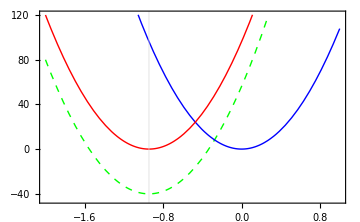

```mathematica
Plot[{U0[x],U1[x],U2[x]},{x,-2,1},Axes->False,Frame->True,PlotStyle->{{Green,Dashed,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]},{Red,AbsoluteThickness[1.0]}},PlotRange->{-45,120},BaseStyle->{FontSize->16,FontFamily->"Helvetica"},FrameStyle->AbsoluteThickness[1.0],ImageSize->Medium,GridLines->{{xm0},None}]
```

Temperature (K):

```mathematica
T=300;
β=1/(kb*T);
```

## Harmonic oscillator energies and wavefunction overlaps

Harmonic energy levels (kcal/mol):

```mathematica
HarmEnergy[n_,f_]:=Module[{omega},
omega=f*cm2au;
au2kcal*omega*(n+1/2)];
```

Harmonic wavefunctions:

```mathematica
HarmWavefunction[n_,f_,x_,OptionsPattern[{M->MassH}]]:=Module[{mu,o,wnorm,w1,w2,q},
mu=OptionValue[M]*Dalton;
o=f*cm2au;
wnorm=((mu*o)/π)^(1/4)*2^(-n/2)*(n!)^(-1/2);
w1=Exp[-1/2 mu*o*x^2];
q=x*Sqrt[mu*o];
w2=HermiteH[n,q];
wnorm*w1*w2];
```

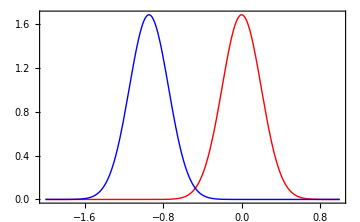

```mathematica
Plot[{HarmWavefunction[0,f1,x],HarmWavefunction[0,f2,x-xm2]},{x,-2,1},PlotRange->All,Axes->True,Frame->True,PlotStyle->{{Red,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]}},FrameStyle->AbsoluteThickness[1.0],BaseStyle->{FontSize->16,FontFamily->"Helvetica"},ImageSize->Medium]
```

Overlap integrals (in this expression the first oscillator is d Bohr to the right of the second one):

```mathematica
HarmOverlap[n1_,n2_,f1_,f2_,d_,OptionsPattern[{M->MassH,Acc->120}]]:=Module[{mass,acc,o1,o2,mu,a1,a2,s,A,Prefactor,b1,b2,i,j,Kaux},
acc=OptionValue[Acc];
mass=SetAccuracy[OptionValue[M],acc];
Kaux[i_,j_,a_,b_]:=SetAccuracy[If[OddQ[i+j],0,(i+j-1)!!/(a+b)^((i+j)/2)],acc];
mu=SetAccuracy[mass*Dalton,acc];
o1=SetAccuracy[f1*cm2au,acc];
o2=SetAccuracy[f2*cm2au,acc];
a1=SetAccuracy[(mu*o1),acc];
a2=SetAccuracy[(mu*o2),acc];
s=SetAccuracy[(a1*a2*d^2)/(a1+a2),acc];
A=SetAccuracy[(2*Sqrt[a1*a2])/(a1+a2),acc];
Prefactor=SetAccuracy[Sqrt[(A*Exp[-s])/(2^(n1+n2)*n1!*n2!)],acc];
b1=SetAccuracy[-((d*a2*Sqrt[a1])/(a1+a2)),acc];
b2=SetAccuracy[(d*a1*Sqrt[a2])/(a1+a2),acc];
Prefactor*Sum[Binomial[n1,i]*Binomial[n2,j]*HermiteH[n1-i,b1]*HermiteH[n2-j,b2]*(2*Sqrt[a1])^i*(2*Sqrt[a2])^j*Kaux[i,j,a1,a2],{j,0,n2},{i,0,n1}]];
```

```mathematica
Accuracy[HarmOverlap[10,21,f1,f2,xm1-xm2]]
```

100.613

## Harmonic bath quantities

```mathematica
λ kcal2au au2cm
```

7200.

Fourier transform of the e^-QS function (in high-T approximation for Debye solvent):

```mathematica
FQSH[ω_]:=Module[{omega,lambda},
omega=ω*cm2au;
lambda=λ*kcal2au;
Sqrt[(π β)/lambda]*Exp[-β(-omega+lambda)^2/(4*lambda)]
];
```

## System setup

Number of reactant and product vibronic states:

```mathematica
Nr=45;
Nk=45;
Ntot=Nr+Nk;
```

Precompute matrices of overlap integrals between reactant and product vibrational wavefunctions:

```mathematica
Clear[SH,SD];
```

```mathematica
Array[SH,{Nr,Nk},{0,0}];
Array[SD,{Nr,Nk},{0,0}];
```

```mathematica
PrintTemporary["In progress..."];
Monitor[k=0;
Do[SH[i,j]=HarmOverlap[i,j,f1H,f2H,xm1-xm2,M->MassH];k++,{i,0,Nr-1},{j,0,Nk-1}],
TableForm[{"<"<>IntegerString[i,10,2]<>"|"<>IntegerString[j,10,2]<>">",
ProgressIndicator[k,{0,Nr*Nk}]},TableDirections->Row]];
```

```mathematica
PrintTemporary["In progress..."];
Monitor[k=0;
Do[SD[i,j]=HarmOverlap[i,j,f1D,f2D,xm1-xm2,M->MassD];k++,{i,0,Nr-1},{j,0,Nk-1}],
TableForm[{"<"<>IntegerString[i,10,2]<>"|"<>IntegerString[j,10,2]<>">",
ProgressIndicator[k,{0,Nr*Nk}]},TableDirections->Row]];
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

## Initial reduced density matrix

#### Vertical excitation from the ground electronic state to the reactant state

```mathematica
σvH=Table[
If[i≤Nr&&j≤Nr,
HarmOverlap[i-1,0,f1H,f0H,xm1-xm0,M->MassH]*HarmOverlap[j-1,0,f1H,f0H,xm1-xm0,M->MassH],0],{i,1,Ntot},{j,1,Ntot}];
```

```mathematica
σvD=Table[
If[i≤Nr&&j≤Nr,
HarmOverlap[i-1,0,f1D,f0D,xm1-xm0,M->MassD]*HarmOverlap[j-1,0,f1D,f0D,xm1-xm0,M->MassD],0],{i,1,Ntot},{j,1,Ntot}];
```

```mathematica
σvdiagH=Table[σvH[[i,i]],{i,1,Ntot}];
```

```mathematica
σvdiagD=Table[σvD[[i,i]],{i,1,Ntot}];
```

```mathematica
Total[σvdiagH]
```

0.999999999999975006366698304241522396036439565318166892720588704329272452616051896195866686116206

```mathematica
Total[σvdiagD]
```

0.999999998366676750454485719289790287262950849659957035941061720226837431155320582605940661

Initial populations:

```mathematica
labellist1=ReplacePart[Table[" ",{i,1,Nr}],Table[i->i-1,{i,1,Nr,5}]];
```

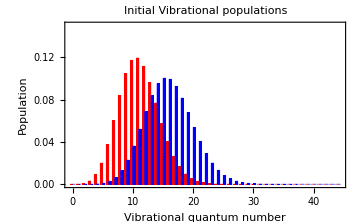

```mathematica
BarChart[{σvdiagH[[Range[1,Nr]]],σvdiagD[[Range[1,Nr]]]},BarStyle->{Red,Blue},PlotRange->{0,0.15},FrameLabel->{"Vibrational quantum number","Population"},PlotLabel->"\nInitial Vibrational populations\n",Axes->False,Frame->True,BarLabels->labellist1,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium,FrameStyle->AbsoluteThickness[1.0]]
```

Initial wavepacket (in the reactant electronic state):

```mathematica
Clear[WavevH,WavevD];
```

```mathematica
WavevH[x_]:=Sum[σvH[[i,j]]*HarmWavefunction[i-1,f1H,x-xm1,M->MassH]*HarmWavefunction[j-1,f1H,x-xm1,M->MassH],{i,1,Nr},{j,1,Nr}];
```

```mathematica
WavevD[x_]:=Sum[σvD[[i,j]]*HarmWavefunction[i-1,f1D,x-xm1,M->MassD]*HarmWavefunction[j-1,f1D,x-xm1,M->MassD],{i,1,Nr},{j,1,Nr}];
```

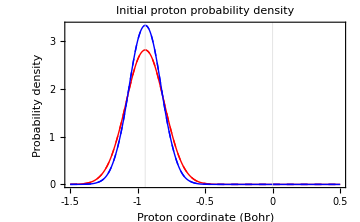

```mathematica
ListLinePlot[{Table[WavevH[x],{x,-1.5,0.5,0.1}],Table[HarmWavefunction[0,f0H,x-xm0,M->MassH]^2,{x,-1.5,0.5,0.1}],Table[WavevD[x],{x,-1.5,0.5,0.1}],Table[HarmWavefunction[0,f0D,x-xm0,M->MassD]^2,{x,-1.5,0.5,0.1}]},PlotRange->All,Axes->False,Frame->True,PlotStyle->{{Red,AbsoluteThickness[1.0]},{Red,Dashed,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]},{Blue,Dashed,AbsoluteThickness[1.0]}},DataRange->{-1.5,0.5},InterpolationOrder->3,GridLines->{{xm0,xm1},{}},FrameLabel->{"Proton coordinate (Bohr)","Probability density"},PlotLabel->"\nInitial proton probability density\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium,FrameStyle->AbsoluteThickness[1.0],FrameTicks->{{{0,1,2,3},None},{{-1.5,-1,-0.5,0,0.5},None}}]
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

```mathematica
labellist1=ReplacePart[Table[" ",{i,1,Nr}],Table[i->i-1,{i,1,Nr,5}]];
```

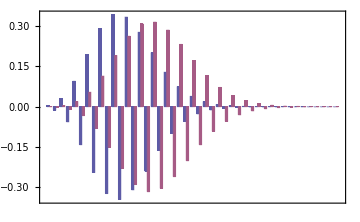

```mathematica
BarChart[{Table[SH[i,0],{i,0,Nr-1}],Table[SD[i,0],{i,0,Nr-1}]},BarLabels->None,Axes->False,Frame->True,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium,FrameStyle->AbsoluteThickness[1.0],FrameTicks->Automatic]
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

## Nonadiabatic transition probabilities

Transition probability from |rμ> to |kν> (forward):

```mathematica
Clear[WforwardH,WforwardD,WbackwardH,WbackwardD]
```

```mathematica
WforwardH[nu_,mu_]:=Module[{emu,enu,o1,o2,s,s2,prefactor,de,integral},
o1=f1H;
o2=f2H;
s=SH[mu,nu];
s2=s^2;
prefactor=(V*kcal2au)^2*s2;
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
de=-(enu-emu)*kcal2au*au2cm;
integral=FQSH[de];
prefactor*integral];
```

```mathematica
WforwardD[nu_,mu_]:=Module[{emu,enu,o1,o2,s,s2,prefactor,de,integral},
o1=f1D;
o2=f2D;
s=SD[mu,nu];
s2=s^2;
prefactor=(V*kcal2au)^2*s2;
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
de=-(enu-emu)*kcal2au*au2cm;
integral=FQSH[de];
prefactor*integral];
```

Transition probability from |kν> to |rμ> (backward):

```mathematica
WbackwardH[mu_,nu_]:=Module[{o1,o2,s,s2,prefactor,emu,enu,de,integral},
o1=f1H;
o2=f2H;
s=SH[mu,nu];
s2=s^2;
prefactor=(V*kcal2au)^2*s2;
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
de=(enu-emu)*kcal2au*au2cm;
integral=FQSH[de];
prefactor*integral];
```

```mathematica
WbackwardD[mu_,nu_]:=Module[{o1,o2,s,s2,prefactor,emu,enu,de,integral},
o1=f1D;
o2=f2D;
s=SD[mu,nu];
s2=s^2;
prefactor=(V*kcal2au)^2*s2;
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
de=(enu-emu)*kcal2au*au2cm;
integral=FQSH[de];
prefactor*integral];
```

Distribution of transition probabilities:

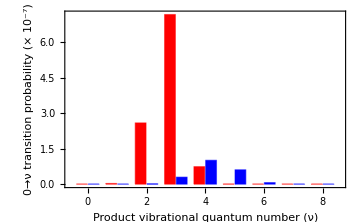

```mathematica
BarChart[{Table[WforwardH[0,i],{i,0,8}]*10^7,Table[WforwardD[0,i]*10^7,{i,0,8}]},Axes->False,Frame->True,FrameLabel->{"Product vibrational quantum number (ν)","0→ν transition probability (× 10^-7)"},BarStyle->{Red,Blue},BarOrientation->Vertical,BarLabels->Range[0,8],BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium,FrameStyle->AbsoluteThickness[1.0],FrameTicks->Automatic]
```

## Additional Redfield tensor components

These are complex-valued functions Γ_μννμ^+ and Γ_μννμ^-:

```mathematica
GammaPlusH[mu_,nu_]:=Module[{emu,enu,o1,o2,s,s2,prefactor1,prefactor2,omega,lambda,z},
lambda=λ*kcal2au;
o1=f1;
o2=f2;
s=SH[mu,nu];
s2=s^2;
prefactor1=(V*kcal2au)^2*s2;
prefactor2=1/2 Sqrt[(π β)/lambda];
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
omega=(emu-enu)*kcal2au;
z=(omega-lambda)/2 Sqrt[β/lambda];
prefactor1*prefactor2*(1+ⅈ Erfi[z])*Exp[-(β (omega-lambda)^2)/(4*lambda)]
];
```

```mathematica
GammaMinusH[mu_,nu_]:=Module[{emu,enu,o1,o2,s,s2,prefactor1,prefactor2,omega,lambda,z},
lambda=λ*kcal2au;
o1=f1;
o2=f2;
s=SH[mu,nu];
s2=s^2;
prefactor1=(V*kcal2au)^2*s2;
prefactor2=1/2 Sqrt[(π β)/lambda];
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
omega=(emu-enu)*kcal2au;
z=(omega-lambda)/2 Sqrt[β/lambda];
prefactor1*prefactor2*(1-ⅈ Erfi[z])*Exp[-(β (omega-lambda)^2)/(4*lambda)]
];
```

```mathematica
GammaPlusD[mu_,nu_]:=Module[{emu,enu,o1,o2,s,s2,prefactor1,prefactor2,omega,lambda,z},
lambda=λ*kcal2au;
o1=f1D;
o2=f2D;
s=SD[mu,nu];
s2=s^2;
prefactor1=(V*kcal2au)^2*s2;
prefactor2=1/2 Sqrt[(π β)/lambda];
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
omega=(emu-enu)*kcal2au;
z=(omega-lambda)/2 Sqrt[β/lambda];
prefactor1*prefactor2*(1+ⅈ Erfi[z])*Exp[-(β (omega-lambda)^2)/(4*lambda)]
];
```

```mathematica
GammaMinusD[mu_,nu_]:=Module[{emu,enu,o1,o2,s,s2,prefactor1,prefactor2,omega,lambda,z},
lambda=λ*kcal2au;
o1=f1D;
o2=f2D;
s=SD[mu,nu];
s2=s^2;
prefactor1=(V*kcal2au)^2*s2;
prefactor2=1/2 Sqrt[(π β)/lambda];
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
omega=(emu-enu)*kcal2au;
z=(omega-lambda)/2 Sqrt[β/lambda];
prefactor1*prefactor2*(1-ⅈ Erfi[z])*Exp[-(β (omega-lambda)^2)/(4*lambda)]
];
```

Coherence relaxation constants:

```mathematica
gammaH[mu1_,mu2_]:=Sum[GammaPlusH[mu1,nu]+GammaMinusH[mu2,nu],{nu,0,Nk-1}];
```

```mathematica
gammaD[mu1_,mu2_]:=Sum[GammaPlusD[mu1,nu]+GammaMinusD[mu2,nu],{nu,0,Nk-1}];
```

```mathematica
gammaH[1,2]
```

1.98348045095500912520374960678724439447086998521×10^-7+2.5533591917553330952842728793842336567410221×10^-6 ⅈ

```mathematica
gammaH[2,1]
```

1.98348045095500912520374960678724439447086998521×10^-7-2.5533591917553330952842728793842336567410221×10^-6 ⅈ

Precompute matrix of gamma's:

```mathematica
Clear[γH,γD]
```

```mathematica
Array[γH,{Nr,Nr}];
Array[γD,{Nr,Nr}];
```

```mathematica
Do[γH[i,j]=0,{i,1,Nr},{j,1,Nr}];
Do[γD[i,j]=0,{i,1,Nr},{j,1,Nr}];
```

```mathematica
PrintTemporary["In progress..."];
Monitor[k=0;
Do[Do[γH[i,j]=gammaH[i-1,j-1];k++,{i,j+1,Nr}],{j,1,Nr-1}],
TableForm[{"Upper triangle: γH ["<>IntegerString[i,10,2]<>", "<>IntegerString[j,10,2]<>"]",
ProgressIndicator[k,{0,(Nr*Nr-Nr)/2}]},TableDirections->Row]
];
```

```mathematica
Do[Do[γH[j,i]=Conjugate[γH[i,j]],{i,j+1,Nr}],{j,1,Nr-1}];
```

```mathematica
TableForm[{γH[31,23],γH[23,31]}]
```

4.8108281228982298763880557959619572278838201486×10^-6-1.38947763098459982584443178146405746328522943×10^-6 ⅈ
4.8108281228982298763880557959619572278838201486×10^-6+1.38947763098459982584443178146405746328522943×10^-6 ⅈ

```mathematica
PrintTemporary["In progress..."];
Monitor[k=0;
Do[Do[γD[i,j]=gammaD[i-1,j-1];k++,{i,j+1,Nr}],{j,1,Nr-1}],
TableForm[{"Upper triangle: γD ["<>IntegerString[i,10,2]<>", "<>IntegerString[j,10,2]<>"]",
ProgressIndicator[k,{0,(Nr*Nr-Nr)/2}]},TableDirections->Row]
];
```

```mathematica
Do[Do[γD[j,i]=Conjugate[γD[i,j]],{i,j+1,Nr}],{j,1,Nr-1}];
```

```mathematica
TableForm[{γD[27,13],γD[13,27]}]
```

9.1938253348411217845789872321530100251624724425×10^-6+2.509053950419155357752528244501827478679531×10^-6 ⅈ
9.1938253348411217845789872321530100251624724425×10^-6-2.509053950419155357752528244501827478679531×10^-6 ⅈ

```mathematica
Clear[k];EmitSound[{Sound[SoundNote["C",1,"Piano"]],Sound[SoundNote["E",1,"Piano"]],Sound[SoundNote["G",2,"Piano"]]}]
```

## Redfield matrices

```mathematica
Clear[RRH,RRD]
```

```mathematica
RRH=
Table[
If[i≤Nr,
If[j≤Nr,If[j≠i,0,-Sum[WforwardH[k,i-1],{k,0,Nk-1}]],WbackwardH[i-1,j-Nr-1]],
If[j≤Nr,WforwardH[i-Nr-1,j-1],If[j≠i,0,-Sum[WbackwardH[m,i-Nr-1],{m,0,Nr-1}]]]],{i,1,Ntot},{j,1,Ntot}];
```

```mathematica
Chop[RRH,10^-30];
```

```mathematica
RRD=
Table[
If[i≤Nr,
If[j≤Nr,If[j≠i,0,-Sum[WforwardD[k,i-1],{k,0,Nk-1}]],WbackwardD[i-1,j-Nr-1]],
If[j≤Nr,WforwardD[i-Nr-1,j-1],If[j≠i,0,-Sum[WbackwardD[m,i-Nr-1],{m,0,Nr-1}]]]],{i,1,Ntot},{j,1,Ntot}];
```

```mathematica
Chop[RRD,10^-30];
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Voice"]],Sound[SoundNote["E",1,"Voice"]],Sound[SoundNote["G",2,"Voice"]]}]
```

```mathematica
Accuracy[RRH]
```

52.4026

## Redfield equations and their solution

### Evolution of populations: direct diagonalization of the Redfield matrix

```mathematica
diagH=Eigensystem[RRH];
evaluesH=diagH[[1]];
MH=Transpose[diagH[[2]]];
MHr=Inverse[MH];
ΛH=DiagonalMatrix[evaluesH];
```

```mathematica
diagD=Eigensystem[RRD];
evaluesD=diagD[[1]];
MD=Transpose[diagD[[2]]];
MDr=Inverse[MD];
ΛD=DiagonalMatrix[evaluesD];
```

```mathematica
Clear[σH,σD]
```

```mathematica
σH[σ0_,t_]:=Module[{Λt,Prop},
Λt=MatrixExp[ΛH t];
Prop=MH . Λt . MHr;
Prop . σ0];
```

```mathematica
σD[σ0_,t_]:=Module[{Λt,Prop},
Λt=MatrixExp[ΛD t];
Prop=MD . Λt . MDr;
Prop . σ0];
```

### Arnoldi iteration method

```mathematica
σAH[Ndim_,σ0_,t_,OptionsPattern[{DebugOutput->False}]]:=Module[{acc,log,norm,i,j,v,u,u1,h,H,V,VT,W,Wr,Λ,diag,dim,normj},
acc=Precision[RRH];
log=OptionValue[DebugOutput];
Array[v,Ndim+1];
Array[u,Ndim+1];
Array[h,{Ndim+1,Ndim+1}];
Array[u1,Ndim+1];
Do[v[i]=0,{i,1,Ndim+1}];
Do[u[i]=0,{i,1,Ndim+1}];
Do[u1[i]=0,{i,1,Ndim+1}];
Do[h[i,j]=0,{i,1,Ndim+1},{j,1,Ndim+1}];
norm=SetPrecision[Norm[σ0],acc];
v[1]=SetPrecision[σ0/norm,acc];
u[1]=SetPrecision[σ0/norm,acc];
For[j=1,j<Ndim+1,j++,
u[j+1]=SetPrecision[RRH . v[j],acc];
For[i=1,i<j+1,i++,h[i,j]=SetPrecision[v[i].u[j+1],acc]];
u1[j+1]=u[j+1]-Sum[SetPrecision[h[k,j]*v[k],acc],{k,1,j}];
normj=SetPrecision[Norm[u1[j+1]],acc];
If[normj<10^-20,Break[],h[j+1,j]=SetPrecision[Norm[u1[j+1]],acc]];
v[j+1]=SetPrecision[u1[j+1]/h[j+1,j],acc]
];
dim=j;
H=Table[h[i,j],{i,1,dim},{j,1,dim}];
VT=Table[v[i],{i,1,dim}];
V=Transpose[VT];
diag=Eigensystem[H];
If[log,Print["Eigenvalues of h-matrix: ",diag[[1]]]];
Λ=DiagonalMatrix[diag[[1]]];
W=Transpose[diag[[2]]];
Wr=Inverse[W];
Chop[SetPrecision[V . W . MatrixExp[Λ t] . Wr . VT . σ0,acc],10^-20]
];
```

```mathematica
σAD[Ndim_,σ0_,t_,OptionsPattern[{DebugOutput->False}]]:=Module[{acc,log,norm,i,j,v,u,u1,h,H,V,VT,W,Wr,Λ,diag,dim,normj},
acc=Precision[RRD];
log=OptionValue[DebugOutput];
Array[v,Ndim+1];
Array[u,Ndim+1];
Array[h,{Ndim+1,Ndim+1}];
Array[u1,Ndim+1];
Do[v[i]=0,{i,1,Ndim+1}];
Do[u[i]=0,{i,1,Ndim+1}];
Do[u1[i]=0,{i,1,Ndim+1}];
Do[h[i,j]=0,{i,1,Ndim+1},{j,1,Ndim+1}];
norm=SetPrecision[Norm[σ0],acc];
v[1]=SetPrecision[σ0/norm,acc];
u[1]=SetPrecision[σ0/norm,acc];
For[j=1,j<Ndim+1,j++,
u[j+1]=SetPrecision[RRD . v[j],acc];
For[i=1,i<j+1,i++,h[i,j]=SetPrecision[v[i].u[j+1],acc]];
u1[j+1]=u[j+1]-Sum[SetPrecision[h[k,j]*v[k],acc],{k,1,j}];
normj=SetPrecision[Norm[u1[j+1]],acc];
If[normj<10^-20,Break[],h[j+1,j]=SetPrecision[Norm[u1[j+1]],acc]];
v[j+1]=SetPrecision[u1[j+1]/h[j+1,j],acc]
];
dim=j;
H=Table[h[i,j],{i,1,dim},{j,1,dim}];
VT=Table[v[i],{i,1,dim}];
V=Transpose[VT];
diag=Eigensystem[H];
If[log,Print["Eigenvalues of h-matrix: ",diag[[1]]]];
Λ=DiagonalMatrix[diag[[1]]];
W=Transpose[diag[[2]]];
Wr=Inverse[W];
Chop[SetPrecision[V . W . MatrixExp[Λ t] . Wr . VT . σ0,acc],10^-20]
];
```

Testing:

```mathematica
Timing@σH[σvdiagH,1ps2au][[1]]
```

{0.95677,0.0002830095836483990429326337729565179702}

```mathematica
Timing@σAH[10,σvdiagH,1ps2au,DebugOutput->False][[1]]
```

{0.381491,0.000283009583647735929507934254647000575274913043}

### Evolution of coherences

Period of oscillations for coherences:

```mathematica
dtH=10(2π)/(f1H*cm2au+Im[γH[1,2]])au2ps
```

0.111178023882975760217894248551441671192279950238

```mathematica
dtD=10(2π)/(f1D*cm2au+Im[γD[1,2]])au2ps
```

0.157192687596845650409513944298313246872923074035

```mathematica
Clear[σcH,σcD]
```

```mathematica
σcH[i_,j_,σcij0_,t_]:=Module[{o1,δω,γ},
o1=f1H*cm2au;
δω=o1*(i-j);
γ=γH[i,j];
σcij0*Exp[-ⅈ*δω*t-γ*t]
];
```

```mathematica
σcD[i_,j_,σcij0_,t_]:=Module[{o1,δω,γ},
o1=f1D*cm2au;
δω=o1*(i-j);
γ=γD[i,j];
σcij0*Exp[-ⅈ*δω*t-γ*t]
];
```

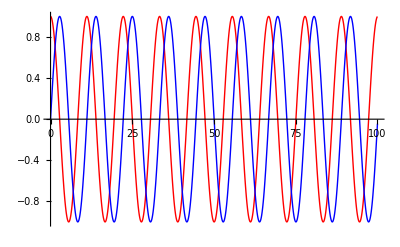

```mathematica
Plot[{Re[σcH[1,2,1.0,t*fs2au]],Im[σcH[1,2,1.0,t*fs2au]]},{t,0,100},PlotRange->All,PlotStyle->{Red,Blue}]
```

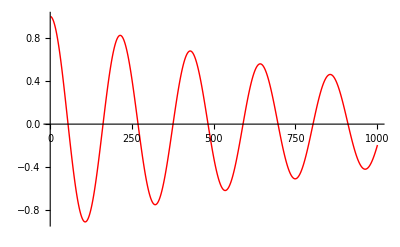

```mathematica
ListLinePlot[Table[Re[σcH[1,3,1.0,(i-1)*dtH* ps2au]],{i,1,1001}],PlotRange->All,PlotStyle->{Red}]
```

### Dynamics of vibrational states populations

```mathematica
labellist=Flatten[{ReplacePart[Table[" ",{i,1,Nr}],Table[i->i-1,{i,1,Nr,10}]],ReplacePart[Table[" ",{i,1,Nk}],Table[i->i-1,{i,1,Nk,10}]]}];
```

```mathematica
Animate[BarChart[{σAH[10,σvdiagH,t*ps2au],σAD[10,σvdiagD,t*ps2au]},BarStyle->{Red,Blue},PlotRange->{0,0.5},FrameLabel->{"Vibrational quantum number","Population"},Axes->False,Frame->True,FrameStyle->AbsoluteThickness[1.0],BarLabels->labellist,PlotLabel->"\nVibrational populations: t = "<>ToString[t]<>" ps\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium,GridLines->{{45},{}}],{{t,0,"Time (ps)"},0,100,1},AnimationRunning->False,AnimationRate->2]
```

### Dynamics of vibrational coherences

```mathematica
Manipulate[BarChart3D[Table[If[i≠j,Re[σcH[i,j,σvH[[i,j]],t*fs2au]],0],{i,1,Nr},{j,1,Nr}],BarStyle->{LightRed},PlotRange->{-0.25,0.25},Axes->True,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{{t,0,"Time (fs)"},0,200,1},FrameLabel->{None,None,"Real parts of vibrational coherences"}]
```

## Dynamics of electronic populations

### State after vertical electronic excitation

```mathematica
σAH[15,σvdiagH,50ps2au];
TableForm[{Sum[%[[i]],{i,1,Nr}],Sum[%[[i]],{i,Nr+1,Ntot}]}]
```

0.499996999465159942129506650242315414242447768
0.500003000534815064237191653999206981793991797

```mathematica
σAD[15,σvdiagD,50ps2au];
TableForm[{Sum[%[[i]],{i,1,Nr}],Sum[%[[i]],{i,Nr+1,Ntot}]}]
```

0.496031309810545190047793967127653026131688253
0.503968688556131560406691752162137261131262652

```mathematica
Print["Tr[σ_H] = ",Total[σAH[15,σvdiagH,100ps2au]]];
```

Tr[σ_H] = 0.999999999999975006366698304241522396036439566

```mathematica
Print["Tr[σ_D] = ",Total[σAD[15,σvdiagD,100ps2au]]];
```

Tr[σ_D] = 0.999999998366676750454485719289790287262950956

#### Precompute the short time evolution (100 fs, every 1 fs; 101 points)

```mathematica
Ntshort=101;
```

```mathematica
PrintTemporary["In progress..."];
σdiagtshortH=Module[{i=0,dt,σprev,σnext,σfull,el1,el2},
σprev=σvdiagH;
σfull={σvdiagH};
dt=fs2au;
Monitor[
For[i=1,i<Ntshort,i++,
σnext=σAH[15,σprev,dt];
σfull=Append[σfull,σnext];
σprev=σnext;
],
TableForm[{"Time: "<>IntegerString[i,10,3]<>" fs",
ProgressIndicator[i,{1,Ntshort}]},TableDirections->Row]
];
σfull
];
```

```mathematica
PrintTemporary["In progress..."];
σdiagtshortD=Module[{i=0,dt,σprev,σnext,σfull,el1,el2},
σprev=σvdiagD;
σfull={σvdiagD};
dt=fs2au;
Monitor[
For[i=1,i<Ntshort,i++,
σnext=σAD[15,σprev,dt];
σfull=Append[σfull,σnext];
σprev=σnext;
],
TableForm[{"Time: "<>IntegerString[i,10,3]<>" fs",
ProgressIndicator[i,{1,Ntshort}]},TableDirections->Row]
];
σfull
];
```

```mathematica
{elv1shortH,elv2shortH}=Module[{el1,el2},
el1=Sum[σdiagtshortH[[All,i]],{i,1,Nr}];
el2=Sum[σdiagtshortH[[All,i]],{i,Nr+1,Ntot}];
{el1,el2}
];
```

```mathematica
{elv1shortD,elv2shortD}=Module[{el1,el2},
el1=Sum[σdiagtshortD[[All,i]],{i,1,Nr}];
el2=Sum[σdiagtshortD[[All,i]],{i,Nr+1,Ntot}];
{el1,el2}
];
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

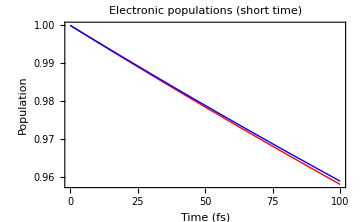

```mathematica
ListLinePlot[{elv1shortH,elv1shortD},PlotRange->All,Axes->False,Frame->True,DataRange->{0,Ntshort-1},PlotStyle->{Red,Blue,Directive[Black,Thin,Dashed]},InterpolationOrder->2,PlotMarkers->None,FrameLabel->{"Time (fs)","Population"},PlotLabel->"\nElectronic populations (short time)\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium,FrameStyle->AbsoluteThickness[1.0]]
```

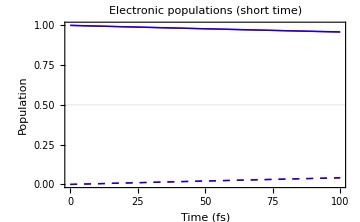

```mathematica
ListLinePlot[{elv1shortH,elv2shortH,elv1shortD,elv2shortD},PlotRange->{0,1},Axes->False,Frame->True,DataRange->{0,Ntshort-1},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}},InterpolationOrder->2,PlotMarkers->None,FrameLabel->{"Time (fs)","Population"},PlotLabel->"\nElectronic populations (short time)\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium,FrameStyle->AbsoluteThickness[1.0],GridLines->{{},{0.5}}]
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

Write out the electronic populations to disk

```mathematica
Export[SystemDialogInput["FileSave"],Table[N[{i-1,elv1shortH[[i]],elv2shortH[[i]],elv1shortD[[i]],elv2shortD[[i]]},12],{i,1,Ntshort}]]
```

/Users/souda/Documents/Projects/Ultrafast_PCET/Data/elpop-sym-bias0-100fs.dat

#### Precompute the long time evolution (every 10 (2π)/(ω+Im[γ]); 201 points)

```mathematica
Ntlong=201;
```

```mathematica
PrintTemporary["In progress..."];
σdiagtlongH=Module[{i,dt,σprev,σnext,σfull,el1,el2},
σprev=σvdiagH;
σfull={σvdiagH};
dt=dtH*ps2au;
Monitor[
For[i=1,i<Ntlong,i++,
σnext=σAH[15,σprev,dt];
σfull=Append[σfull,σnext];
σprev=σnext;
],
TableForm[{"Time: "<>ToString[PaddedForm[i*dtH,{8,3}]]<>" ps",
ProgressIndicator[i,{1,Ntlong}]},TableDirections->Row]
];
σfull
];
```

```mathematica
PrintTemporary["In progress..."];
σdiagtlongD=Module[{i,dt,σprev,σnext,σfull,el1,el2},
σprev=σvdiagD;
σfull={σvdiagD};
dt=dtD*ps2au;
Monitor[
For[i=1,i<Ntlong,i++,
σnext=σAD[15,σprev,dt];
σfull=Append[σfull,σnext];
σprev=σnext;
],
TableForm[{"Time: "<>ToString[PaddedForm[i*dtD,{8,3}]]<>" ps",
ProgressIndicator[i,{1,Ntlong}]},TableDirections->Row]
];
σfull
];
```

```mathematica
{elv1longH,elv2longH}=Module[{el1,el2},
el1=Sum[σdiagtlongH[[All,i]],{i,1,Nr}];
el2=Sum[σdiagtlongH[[All,i]],{i,Nr+1,Ntot}];
{el1,el2}
];
```

```mathematica
{elv1longD,elv2longD}=Module[{el1,el2},
el1=Sum[σdiagtlongD[[All,i]],{i,1,Nr}];
el2=Sum[σdiagtlongD[[All,i]],{i,Nr+1,Ntot}];
{el1,el2}
];
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

Number of points to plot:

```mathematica
Ntmax=101;If[Ntmax>Ntlong,Print["Must be smaller than ",Ntlong,", has been set to ",Ntlong]];
```

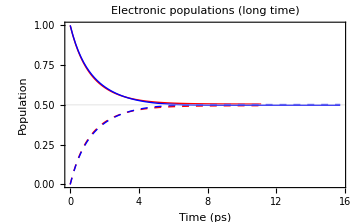

```mathematica
ListLinePlot[{Table[{(i-1)*dtH,elv1longH[[i]]},{i,1,Ntmax}],Table[{(i-1)*dtH,elv2longH[[i]]},{i,1,Ntmax}],Table[{(i-1)*dtD,elv1longD[[i]]},{i,1,Ntmax}],Table[{(i-1)*dtD,elv2longD[[i]]},{i,1,Ntmax}]},PlotRange->{0,1},Axes->False,Frame->True,PlotStyle->{{Red,AbsoluteThickness[1.0]},{Red,Dashed,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]},{Blue,Dashed,AbsoluteThickness[1.0]}},InterpolationOrder->1,PlotMarkers->None,FrameLabel->{"Time (ps)","Population"},PlotLabel->"\nElectronic populations (long time)\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameStyle->AbsoluteThickness[1.0],ImageSize->Medium,GridLines->{{},{0.5}}]
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

Write out the electronic populations to disk

```mathematica
Export[SystemDialogInput["FileSave"],Table[N[{(i-1)dtH,elv1longH[[i]],elv2longH[[i]]},12],{i,1,Ntlong}],"Table"]
```

/Users/souda/Documents/Projects/Ultrafast_PCET/Data/elpop-sym-bias0-20ps-H.dat

```mathematica
Export[SystemDialogInput["FileSave"],Table[N[{(i-1)dtD,elv1longD[[i]],elv2longD[[i]]},12],{i,1,Ntlong}],"Table"]
```

/Users/souda/Documents/Projects/Ultrafast_PCET/Data/elpop-sym-bias0-30ps-D.dat

## Dynamics of the proton vibrational wavepackets

Precompute vibrational wavefunctions on a predefined grid:

```mathematica
xlist=Table[x,{x,-2.0,2.0,0.1}];
```

```mathematica
Nx=41;
```

```mathematica
wflist1H=Table[HarmWavefunction[i-1,f1H,xlist[[k]]-xm1,M->MassH],{i,1,Nr},{k,1,Nx}];
```

```mathematica
wflist1D=Table[HarmWavefunction[i-1,f1D,xlist[[k]]-xm1,M->MassD],{i,1,Nr},{k,1,Nx}];
```

```mathematica
wflist2H=Table[HarmWavefunction[i-1,f2H,xlist[[k]]-xm2,M->MassH],{i,1,Nk},{k,1,Nx}];
```

```mathematica
wflist2D=Table[HarmWavefunction[i-1,f2D,xlist[[k]]-xm2,M->MassD],{i,1,Nk},{k,1,Nx}];
```

### Short time evolution

Precompute vibrational wavepackets for short time evolution:

```mathematica
Clear[WPshortv1diagH,WPshortv1coherH,WPshortv1H,WPshortv2H,WPshortv1diagD,WPshortv1coherD,WPshortv1D,WPshortv2D]
```

```mathematica
PrintTemporary["In progress..."];
Monitor[WPshortv1diagH=
Table[Sum[σdiagtshortH[[t,i]]*wflist1H[[i,k]]^2,{i,1,Nr}],{t,1,Ntshort,1},{k,1,Nx}],
TableForm[{"Time: "<>IntegerString[t-1,10,3]<>" fs; Proton grid point: "<>IntegerString[k,10,2]<>">",
ProgressIndicator[(t-1)Nx+k,{1,Ntshort*Nx}]},TableDirections->Row]
];
```

```mathematica
PrintTemporary["In progress..."];
Monitor[
WPshortv1coherH=
Table[
Sum[Sum[2Re[σcH[i,j,σvH[[i,j]],(t-1)*fs2au]]*wflist1H[[i,k]]*wflist1H[[j,k]],{i,j+1,Nr}],{j,1,Nr}],{t,1,Ntshort},{k,1,Nx}],
TableForm[{"Time: "<>ToString[PaddedForm[(t-1),{8,3}]]<>" fs; Proton grid point: "<>IntegerString[k,10,2],
ProgressIndicator[(t-1)Nx+k,{1,Ntshort*Nx}]},TableDirections->Row]
];
```

```mathematica
WPshortv1H=WPshortv1diagH+WPshortv1coherH;
```

```mathematica
PrintTemporary["In progress..."];
Monitor[
WPshortv2H=
Table[
Sum[σdiagtshortH[[t,i]]*wflist2H[[i-Nr,k]]^2,{i,Nr+1,Ntot}],{t,1,Ntshort,1},{k,1,Nx}],
TableForm[{"Time: "<>IntegerString[t-1,10,3]<>" fs; Proton grid point: "<>IntegerString[k,10,2],
ProgressIndicator[(t-1)Nx+k,{1,Ntshort*Nx}]},TableDirections->Row]
];
```

```mathematica
PrintTemporary["In progress..."];
Monitor[WPshortv1diagD=
Table[
Sum[σdiagtshortD[[t,i]]*wflist1D[[i,k]]^2,{i,1,Nr}],{t,1,Ntshort,1},{k,1,Nx}],
TableForm[{"Time: "<>IntegerString[t-1,10,3]<>" fs; Proton grid point: "<>IntegerString[k,10,2],
ProgressIndicator[(t-1)Nx+k,{1,Ntshort*Nx}]},TableDirections->Row]
];
```

```mathematica
PrintTemporary["In progress..."];
Monitor[
WPshortv1coherD=
Table[
Sum[Sum[2Re[σcD[i,j,σvD[[i,j]],(t-1)*fs2au]]*wflist1D[[i,k]]*wflist1D[[j,k]],{i,j+1,Nr}],{j,1,Nr}],{t,1,Ntshort},{k,1,Nx}],
TableForm[{"Time: "<>ToString[PaddedForm[(t-1),{8,3}]]<>" fs; Proton grid point: "<>IntegerString[k,10,2],
ProgressIndicator[(t-1)Nx+k,{1,Ntshort*Nx}]},TableDirections->Row]
];
```

```mathematica
WPshortv1D=WPshortv1diagD+WPshortv1coherD;
```

```mathematica
PrintTemporary["In progress..."];
Monitor[WPshortv2D=Table[
Sum[σdiagtshortD[[t,i]]*wflist2D[[i-Nr,k]]^2,{i,Nr+1,Ntot}],{t,1,Ntshort,1},{k,1,Nx}],
TableForm[{"Time: "<>IntegerString[t-1,10,3]<>" fs; Proton grid point: "<>IntegerString[k,10,2],
ProgressIndicator[(t-1)Nx+k,{1,Ntshort*Nx}]},TableDirections->Row]
];
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["C",2,"Flute"]],Sound[SoundNote["B",0.5,"Flute"]],Sound[SoundNote["C",2,"Flute"]]}]
```

```mathematica
Animate[ListLinePlot[{Re@WPshortv1diagH[[t,All]],Re@WPshortv1diagD[[t,All]],Re@WPshortv2H[[t,All]],Re@WPshortv2D[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1.0]},{Red,Dashed,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]},{Blue,Dashed,AbsoluteThickness[1.0]}},PlotRange->{0,1},DataRange->{-2,2},Axes->{False,True},Frame->True,FrameLabel->{"Proton coordinate (Bohr)","Probability"},PlotLabel->"\nDiagonal part\nof the wave packet: t = "<>ToString[t]<>" fs\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium,FrameStyle->AbsoluteThickness[1.0]],{t,1,Ntshort,1},AnimationRunning->False,DisplayAllSteps->True,AnimationRate->10]
```

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_wp-diag-100fs.gif",Table[ListLinePlot[{Re@WPshortv1diagH[[t,All]],Re@WPshortv1diagD[[t,All]],Re@WPshortv2H[[t,All]],Re@WPshortv2D[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1.0]},{Red,Dashed,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]},{Blue,Dashed,AbsoluteThickness[1.0]}},PlotRange->{0,1},DataRange->{-2,2},Axes->{False,True},Frame->True,FrameStyle->AbsoluteThickness[1.0],FrameLabel->{"Proton coordinate (Bohr)","Probability"},PlotLabel->"\nDiagonal part\nof the wave packet: t = "<>ToString[t]<>" fs\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,101,1}],"GIF"]
```

06-09-09-02-18-05_sym-bias0_wp-diag-100fs.gif

```mathematica
Animate[ListLinePlot[{Re@WPshortv1coherH[[t,All]],Re@WPshortv1coherD[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1.0]},{Red,Dashed,AbsoluteThickness[1.0]}},PlotRange->{-1,3},DataRange->{-2,2},Axes->{True,True},Frame->True,FrameLabel->{"Proton coordinate (Bohr)","Probability"},FrameStyle->AbsoluteThickness[1.0],PlotLabel->"\nCoherent part\nof the wave packet: t = "<>ToString[t]<>" fs\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,Ntshort,1},AnimationRunning->False,DisplayAllSteps->True,AnimationRate->10]
```

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_wp-coher-100fs.gif",Table[ListLinePlot[{Re@WPshortv1coherH[[t,All]],Re@WPshortv1coherD[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1.0]},{Red,Dashed,AbsoluteThickness[1.0]}},PlotRange->{-1,3},DataRange->{-2,2},Axes->{True,True},Frame->True,FrameStyle->AbsoluteThickness[1.0],FrameLabel->{"Proton coordinate (Bohr)","Probability"},PlotLabel->"\nCoherent part\nof the wave packet: t = "<>ToString[t]<>" fs",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,Ntshort,1}],"GIF"]
```

06-09-09-02-18-32_sym-bias0_wp-coher-100fs.gif

```mathematica
Animate[ListLinePlot[{Re@WPshortv1H[[t,All]],Re@WPshortv2H[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]}},PlotRange->{-0.5,3.5},DataRange->{-2,2},Axes->{True,True},Frame->True,FrameLabel->{"Proton coordinate (Bohr)","Density"},FrameStyle->AbsoluteThickness[1.0],PlotLabel->"\nTotal wave packet: t = "<>ToString[t]<>" fs\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,Ntshort,1},AnimationRunning->False,DisplayAllSteps->True,AnimationRate->10]
```

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_wp-total-100fs-H.gif",Table[ListLinePlot[{Re@WPshortv1H[[t,All]],Re@WPshortv2H[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]}},PlotRange->{-0.5,3.5},DataRange->{-2,2},Axes->{True,True},Frame->True,FrameLabel->{"Proton coordinate (Bohr)","Density"},FrameStyle->AbsoluteThickness[1.0],PlotLabel->"\nTotal wave packet: t = "<>ToString[t]<>" fs\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,101,1}],"GIF"]
```

06-09-09-02-18-51_sym-bias0_wp-total-100fs-H.gif

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_wp-total-100fs-D.gif",Table[ListLinePlot[{Re@WPshortv1D[[t,All]],Re@WPshortv2D[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]}},PlotRange->{-0.5,3.5},DataRange->{-2,2},Axes->{True,True},Frame->True,FrameLabel->{"Proton coordinate (Bohr)","Density"},FrameStyle->AbsoluteThickness[1.0],PlotLabel->"\nTotal wave packet: t = "<>ToString[t]<>" fs\n",BaseStyle->{FontSize->18,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,101,1}],"GIF"]
```

06-09-09-02-19-11_sym-bias0_wp-total-100fs-D.gif

-------------------------- 3D-plots:

```mathematica
TableForm[{ListPlot3D[Re@WPshortv1H[[Range[1,21],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-2,2},{0,20}},AxesLabel->{"","",""},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Mesh->{0,19},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},AxesStyle->AbsoluteThickness[1],BoundaryStyle->None,ImageSize->Medium],
ListPlot3D[Re@WPshortv2H[[Range[1,21],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-2,2},{0,20}},AxesLabel->{"","",""},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Mesh->{0,19},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},AxesStyle->AbsoluteThickness[1],BoundaryStyle->None,ImageSize->Medium]},
TableDirections->Row]
```

-Graphics3D- | -Graphics3D-

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_wp1-3d-20fs-H.pdf",
ListPlot3D[Re@WPshortv1H[[Range[1,21],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-2,2},{0,20}},AxesLabel->{"","",""},AxesStyle->AbsoluteThickness[1],BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Mesh->{0,19},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},BoundaryStyle->None,ImageSize->Medium],
"PDF"]
```

06-09-09-02-19-35_sym-bias0_wp1-3d-20fs-H.pdf

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_wp2-3d-20fs-H.pdf",
ListPlot3D[Re@WPshortv2H[[Range[1,21],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-2,2},{0,20}},AxesLabel->{"","",""},AxesStyle->AbsoluteThickness[1],BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Mesh->{0,19},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},BoundaryStyle->None,ImageSize->Medium],
"PDF"]
```

06-09-09-02-19-36_sym-bias0_wp2-3d-20fs-H.pdf

```mathematica
TableForm[{ListPlot3D[Re@WPshortv1D[[Range[1,21],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-1.5,1.5},{0,20}},AxesLabel->{"","",""},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Mesh->{0,19},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},AxesStyle->AbsoluteThickness[1],BoundaryStyle->None,ImageSize->Medium],
ListPlot3D[Re@WPshortv2D[[Range[1,21],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-1.5,1.5},{0,20}},AxesLabel->{"","",""},AxesStyle->AbsoluteThickness[1],BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Mesh->{0,19},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},BoundaryStyle->None,ImageSize->Medium]},
TableDirections->Row]
```

-Graphics3D- | -Graphics3D-

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_wp1-3d-20fs-D.pdf",
ListPlot3D[Re@WPshortv1D[[Range[1,21],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-2,2},{0,20}},AxesLabel->{"","",""},AxesStyle->AbsoluteThickness[1],BaseStyle->{FontSize->12,FontFamily->"Helvetica"},Mesh->{0,19},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},BoundaryStyle->None,ImageSize->Medium],
"PDF"]
```

06-09-09-02-19-39_sym-bias0_wp1-3d-20fs-D.pdf

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_wp2-3d-20fs-D.pdf",
ListPlot3D[Re@WPshortv2D[[Range[1,21],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-2,2},{0,20}},AxesLabel->{"","",""},AxesStyle->AbsoluteThickness[1],BaseStyle->{FontSize->12,FontFamily->"Helvetica"},Mesh->{0,19},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},BoundaryStyle->None,ImageSize->Medium],
"PDF"]
```

06-09-09-02-19-40_sym-bias0_wp2-3d-20fs-D.pdf

### Long time evolution

Precompute vibrational wavepackets for long time evolution:

```mathematica
Monitor[WPlongv1diagH=
Table[
Sum[σdiagtlongH[[t,i]]*wflist1H[[i,k]]^2,{i,1,Nr}],{t,1,Ntlong,1},{k,1,Nx}],
TableForm[{"Time: "<>ToString[PaddedForm[(t-1)*dtH,{8,3}]]<>" ps; Proton grid point: "<>IntegerString[k,10,2],
ProgressIndicator[(t-1)Nx+k,{1,Ntlong*Nx}]},TableDirections->Row]
];
```

```mathematica
PrintTemporary["In progress..."];
Monitor[
WPlongv1coherH=
Table[
Sum[Sum[2Re[σcH[i,j,σvH[[i,j]],(t-1)*dtH*ps2au]]*wflist1H[[i,k]]*wflist1H[[j,k]],{i,j+1,Nr}],{j,1,Nr}],{t,1,Ntlong},{k,1,Nx}],
TableForm[{"Time: "<>ToString[PaddedForm[(t-1)*dtH,{8,3}]]<>" ps; Proton grid point: "<>IntegerString[k,10,2],
ProgressIndicator[(t-1)Nx+k,{1,Ntlong*Nx}]},TableDirections->Row]
];
```

```mathematica
WPlongv1H=WPlongv1diagH+WPlongv1coherH;
```

```mathematica
Monitor[WPlongv2H=Table[
Sum[σdiagtlongH[[t,i]]*wflist2H[[i-Nr,k]]^2,{i,Nr+1,Ntot}],{t,1,Ntlong,1},{k,1,Nx}],
TableForm[{"Time: "<>ToString[PaddedForm[(t-1)*dtH,{8,3}]]<>" ps; Proton grid point: "<>IntegerString[k,10,2],
ProgressIndicator[(t-1)Nx+k,{1,Ntlong*Nx}]},TableDirections->Row]
];
```

```mathematica
Monitor[WPlongv1diagD=
Table[
Sum[σdiagtlongD[[t,i]]*wflist1D[[i,k]]^2,{i,1,Nr}],{t,1,Ntlong,1},{k,1,Nx}],
TableForm[{"Time: "<>ToString[PaddedForm[(t-1)*dtD,{8,3}]]<>" ps; Proton grid point: "<>IntegerString[k,10,2],
ProgressIndicator[(t-1)Nx+k,{1,Ntlong*Nx}]},TableDirections->Row]
];
```

```mathematica
PrintTemporary["In progress..."];
Monitor[
WPlongv1coherD=
Table[
Sum[Sum[2Re[σcD[i,j,σvD[[i,j]],(t-1)*dtD*ps2au]]*wflist1D[[i,k]]*wflist1D[[j,k]],{i,j+1,Nr}],{j,1,Nr}],{t,1,Ntlong},{k,1,Nx}],
TableForm[{"Time: "<>ToString[PaddedForm[(t-1)*dtD,{8,3}]]<>" ps; Proton grid point: "<>IntegerString[k,10,2],
ProgressIndicator[(t-1)Nx+k,{1,Ntlong*Nx}]},TableDirections->Row]
];
```

```mathematica
WPlongv1D=WPlongv1diagD+WPlongv1coherD;
```

```mathematica
Monitor[WPlongv2D=Table[
Sum[σdiagtlongD[[t,i]]*wflist2D[[i-Nr,k]]^2,{i,Nr+1,Ntot}],{t,1,Ntlong,1},{k,1,Nx}],
TableForm[{"Time: "<>ToString[PaddedForm[(t-1)*dtD,{8,3}]]<>" ps; Proton grid point: "<>IntegerString[k,10,2],
ProgressIndicator[(t-1)Nx+k,{1,Ntlong*Nx}]},TableDirections->Row]
];
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["C",2,"Flute"]],Sound[SoundNote["B",0.5,"Flute"]],Sound[SoundNote["C",2,"Flute"]]}]
```

```mathematica
Ntmax=201;If[Ntmax>Ntlong,Print["Must be smaller than ",Ntlong,", has been set to ",Ntlong]];
```

```mathematica
Animate[ListLinePlot[{Re@WPlongv1diagH[[t,All]],Re@WPlongv2H[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1]},{Blue,AbsoluteThickness[1]}},PlotRange->{0,1},DataRange->{-2,2},Axes->{False,True},Frame->True,FrameStyle->AbsoluteThickness[1],FrameLabel->{"Proton coordinate (Bohr)","Density"},PlotLabel->"\nDiagonal part\nof the H wave packet: t = "<>ToString[PaddedForm[(t-1)*dtH,{8,3}]]<>" ps\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,Ntlong,1},AnimationRunning->False,DisplayAllSteps->True,AnimationRate->10]
```

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_WP-diag-20ps-H.gif",Table[ListLinePlot[{Re@WPlongv1diagH[[t,All]],Re@WPlongv2H[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1]},{Blue,AbsoluteThickness[1]}},PlotRange->{0,1},DataRange->{-2,2},Axes->{False,True},Frame->True,FrameStyle->AbsoluteThickness[1],FrameLabel->{"Proton coordinate (Bohr)","Probability"},PlotLabel->"\nDiagonal part\nof the H wave packet: t = "<>ToString[PaddedForm[(t-1)*dtH,{8,3}]]<>" ps\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,Ntmax,1}],"GIF"]
```

06-09-09-02-54-51_sym-bias0_WP-diag-20ps-H.gif

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_WP-diag-30ps-D.gif",Table[ListLinePlot[{Re@WPlongv1diagD[[t,All]],Re@WPlongv2D[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1]},{Blue,AbsoluteThickness[1]}},PlotRange->{0,1},DataRange->{-2,2},Axes->{False,True},Frame->True,FrameStyle->AbsoluteThickness[1],FrameLabel->{"Proton coordinate (Bohr)","Probability"},PlotLabel->"\nDiagonal part\nof the D wave packet: t = "<>ToString[PaddedForm[(t-1)*dtH,{8,3}]]<>" ps\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,Ntmax,1}],"GIF"]
```

06-09-09-02-55-46_sym-bias0_WP-diag-30ps-D.gif

```mathematica
Animate[ListLinePlot[{WPlongv1coherH[[t,All]]},InterpolationOrder->2,PlotStyle->{Red,AbsoluteThickness[1]},PlotRange->{-1,3},DataRange->{-2,2},Axes->{True,True},Frame->True,FrameLabel->{"Proton coordinate (Bohr)","Probability"},FrameStyle->AbsoluteThickness[1],PlotLabel->"\nCoherent part\nof the wave packet: t = "<>ToString[PaddedForm[(t-1)*dtH,{8,3}]]<>" ps\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,Ntlong,1},AnimationRunning->False,DisplayAllSteps->True,AnimationRate->5]
```

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_WP-coher-20ps-H.gif",Table[ListLinePlot[{Re@WPlongv1coherH[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1]},{Red,Dashed,AbsoluteThickness[1]}},PlotRange->{-1,3},DataRange->{-2,2},Axes->{True,True},Frame->True,FrameStyle->AbsoluteThickness[1],FrameLabel->{"Proton coordinate (Bohr)","Probability"},PlotLabel->"\nCoherent part\nof the H wave packet: t = "<>ToString[PaddedForm[(t-1)*dtH,{8,3}]]<>" ps\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,Ntlong,1}],"GIF"]
```

06-09-09-02-56-23_sym-bias0_WP-coher-20ps-H.gif

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_WP-coher-30ps-D.gif",Table[ListLinePlot[{Re@WPlongv1coherD[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1]},{Red,Dashed,AbsoluteThickness[1]}},PlotRange->{-1,3},DataRange->{-2,2},Axes->{True,True},Frame->True,FrameStyle->AbsoluteThickness[1],FrameLabel->{"Proton coordinate (Bohr)","Probability"},PlotLabel->"\nCoherent part of the D wave packet: t = "<>ToString[PaddedForm[(t-1)*dtH,{8,3}]]<>" ps\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,Ntlong,1}],"GIF"]
```

06-09-09-02-56-58_sym-bias0_WP-coher-30ps-D.gif

```mathematica
Animate[ListLinePlot[{Re@WPlongv1H[[t,All]],Re@WPlongv2H[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1]},{Blue,AbsoluteThickness[1]}},PlotRange->{-0.5,3.5},DataRange->{-2,2},Axes->{True,True},Frame->True,FrameStyle->AbsoluteThickness[1],FrameLabel->{"Proton coordinate (Bohr)","Probability"},PlotLabel->"\nTotal H wave packet: t = "<>ToString[PaddedForm[(t-1)*dtH,{8,3}]]<>" ps\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,Ntlong,1},AnimationRunning->False,DisplayAllSteps->True,AnimationRate->5]
```

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_WPH-total-20ps.gif",Table[ListLinePlot[{Re@WPlongv1H[[t,All]],Re@WPlongv2H[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1]},{Blue,AbsoluteThickness[1]}},PlotRange->{-0.5,3.5},DataRange->{-2,2},Axes->{True,True},Frame->True,FrameStyle->AbsoluteThickness[1],FrameLabel->{"Proton coordinate (Bohr)","Probability"},PlotLabel->"\nTotal H wave packet: t = "<>ToString[PaddedForm[(t-1)*dtH,{8,3}]]<>" ps\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,Ntlong,1}],"GIF"]
```

06-09-09-02-57-33_sym-bias0_WPH-total-20ps.gif

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_WPD-total-30ps.gif",Table[ListLinePlot[{Re@WPlongv1D[[t,All]],Re@WPlongv2D[[t,All]]},InterpolationOrder->2,PlotStyle->{{Red,AbsoluteThickness[1]},{Blue,AbsoluteThickness[1]}},PlotRange->{-0.5,3.5},DataRange->{-2,2},Axes->{True,True},Frame->True,FrameStyle->AbsoluteThickness[1],FrameLabel->{"Proton coordinate (Bohr)","Probability"},PlotLabel->"\nTotal D wave packet: t = "<>ToString[PaddedForm[(t-1)*dtH,{8,3}]]<>" ps\n",BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->Medium],{t,1,Ntlong,1}],"GIF"]
```

06-09-09-02-58-20_sym-bias0_WPD-total-30ps.gif

-------------------------- 3D-plots:

```mathematica
TableForm[{ListPlot3D[Re@WPlongv1H[[Range[1,101],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-2,2},{0,100dtH}},AxesLabel->{"","",""},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Mesh->{0,25},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},AxesStyle->AbsoluteThickness[1],BoundaryStyle->None,ImageSize->Medium],
ListPlot3D[Re@WPlongv2H[[Range[1,101],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-2,2},{0,100dtH}},AxesLabel->{"","",""},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Mesh->{0,25},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},AxesStyle->AbsoluteThickness[1],BoundaryStyle->None,ImageSize->Medium]},
TableDirections->Row]
```

-Graphics3D- | -Graphics3D-

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_WP1-3d-10ps-H.pdf",
ListPlot3D[WPlongv1H[[Range[1,101],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-2,2},{0,100dtH}},AxesLabel->{"","",""},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Mesh->{0,25},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},AxesStyle->AbsoluteThickness[1],BoundaryStyle->None,ImageSize->Medium],
"PDF"]
```

06-09-09-03-01-10_sym-bias0_WP1-3d-10ps-H.pdf

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_WP2-3d-10ps-H.pdf",
ListPlot3D[WPlongv2H[[Range[1,101],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-2,2},{0,100dtH}},AxesLabel->{"","",""},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Mesh->{0,25},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},AxesStyle->AbsoluteThickness[1],BoundaryStyle->None,ImageSize->Medium],
"PDF"]
```

06-09-09-03-01-19_sym-bias0_WP2-3d-10ps-H.pdf

```mathematica
TableForm[{ListPlot3D[WPlongv1D[[Range[1,101],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-2,2},{0,100dtD}},AxesLabel->{"","",""},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Mesh->{0,25},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},AxesStyle->AbsoluteThickness[1],BoundaryStyle->None,ImageSize->Medium],
ListPlot3D[WPlongv2D[[Range[1,101],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-2,2},{0,100dtD}},AxesLabel->{"","",""},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Mesh->{0,25},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},AxesStyle->AbsoluteThickness[1],BoundaryStyle->None,ImageSize->Medium]},
TableDirections->Row]
```

-Graphics3D- | -Graphics3D-

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_WP1-3d-15ps-D.pdf",
ListPlot3D[WPlongv1D[[Range[1,101],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-2,2},{0,100dtD}},AxesLabel->{"","",""},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Mesh->{0,25},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},AxesStyle->AbsoluteThickness[1],BoundaryStyle->None,ImageSize->Medium],
"PDF"]
```

06-09-09-03-01-58_sym-bias0_WP1-3d-15ps-D.pdf

```mathematica
Export[Timestamp<>"_"<>Modelname<>"_WP2-3d-15ps-D.tiff",
ListPlot3D[WPlongv2D[[Range[1,101],All]],PlotRange->All,InterpolationOrder->2,DataRange->{{-2,2},{0,100dtD}},AxesLabel->{"","",""},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Mesh->{0,25},MeshShading->None,MeshStyle->{Black,AbsoluteThickness[1]},PlotStyle->None,PlotRange->All,Boxed->False,Axes->{True,True,False},AxesStyle->AbsoluteThickness[1],BoundaryStyle->None,ImageSize->Medium],
"PDF"]
```

06-09-09-03-02-01_sym-bias0_WP2-3d-15ps-D.tiff